```mathematica
Assuming[r>0,Simplify[((7 7^(2/3) α^2-108 7^(2/3) β^2+7 α ((49 r^6 α^3-1134 r^6 α β^2+54 √21 √(r^12 β^4 (-7 α^2+144 β^2)))/r^6)^(1/3)+7^(1/3) ((49 r^6 α^3-1134 r^6 α β^2+54 √21 √(r^12 β^4 (-7 α^2+144 β^2)))/r^6)^(2/3)) r^2)/(36 β^2 ((49 r^6 α^3-1134 r^6 α β^2+54 √21 √(r^12 β^4 (-7 α^2+144 β^2)))/r^6)^(1/3))]]
```

(r^2 (7 7^(2/3) α^2-108 7^(2/3) β^2+7 α (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(1/3)+7^(1/3) (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(2/3)))/(36 β^2 (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(1/3))

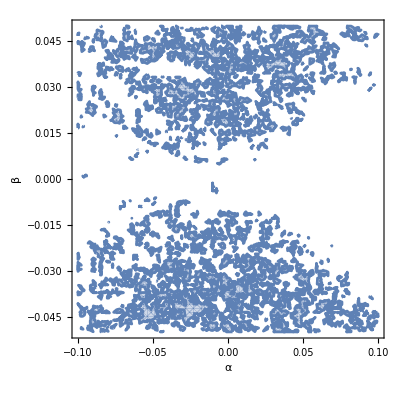

```mathematica
RegionPlot[7 7^(2/3) α^2-108 7^(2/3) β^2+7 α (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(1/3)+7^(1/3) (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(2/3)==0,{α,-0.1,0.1},{β,-0.05,0.05},PlotPoints->40,FrameLabel->{"α","β"}]
```

```mathematica
Clear[μ]
```

```mathematica
ff:=-(-7 r^2 α-36 β^2)/(36 β^2)-(-49 r^4 α^2+756 r^4 β^2)/(18 2^(2/3) β^2 (686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3))+1/(36 2^(1/3) β^2)(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3)
```

```mathematica
Simplify[Assuming[α>0 && β!=1/6 √(7/3) α&&β>0&& r>0 &&μ>0,Series[ff,{r,0,2}]]]
```

1+((7/3)^(1/3) (7 α^2-108 β^2) (α+μ)^(1/3) r^(2/3))/(2^(2/3) β^(2/3) ((-7 α^2+108 β^2)^3)^(1/3))+(7 α r^2)/(36 β^2)+O[r]^(7/3)

```mathematica
dff:=Simplify[D[ff,r]]
```

```mathematica
Simplify[Assuming[α>0 && β!=1/6 √(7/3) α&&β>0&& r>0 &&μ>0,Series[dff,{r,0,2}]]]
```

((14/3)^(1/3) (7 α^2-108 β^2) (α+μ)^(1/3))/(3 β^(2/3) ((-7 α^2+108 β^2)^3)^(1/3) r^(1/3))+(7 α r)/(18 β^2)+O[r]^(7/3)

```mathematica
Simplify[(((7/3)^(1/3) (7 α^2-108 β^2) (α+μ)^(1/3))/(2^(2/3) β^(2/3) ((-7 α^2+108 β^2)^3)^(1/3)))/(((14/3)^(1/3) (7 α^2-108 β^2) (α+μ)^(1/3))/(3 β^(2/3) ((-7 α^2+108 β^2)^3)^(1/3)))]
```

3/2

```mathematica
Assuming[α>0 &&β>0&& r>0 &&μ>0&&r ∈ Reals,Solve[ff==0,μ]]
```

$Aborted

```mathematica
Reduce[0<(α+μ)/β^2<12/7&&β!=0&&7 α^2!=108 β^2,{α,β},Reals]
```

(μ<-9/4&&α>-μ&&(β<-1/6 √(7/3) √(α^2)||-1/6 √(7/3) √(α^2)<β<-1/2 √(7/3) √(α+μ)||1/2 √(7/3) √(α+μ)<β<1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))||(μ==-9/4&&((9/4<α<9/2&&(β<-1/6 √(7/3) √(α^2)||-1/6 √(7/3) √(α^2)<β<-1/2 √(7/3) √(-9/4+α)||1/2 √(7/3) √(-9/4+α)<β<1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))||(α==9/2&&(β<-(√21)/4||β>(√21)/4))||(α>9/2&&(β<-1/6 √(7/3) √(α^2)||-1/6 √(7/3) √(α^2)<β<-1/2 √(7/3) √(-9/4+α)||1/2 √(7/3) √(-9/4+α)<β<1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))))||(-9/4<μ<0&&((-μ<α<9/2-3/2 √(9+4 μ)&&(β<-1/6 √(7/3) √(α^2)||-1/6 √(7/3) √(α^2)<β<-1/2 √(7/3) √(α+μ)||1/2 √(7/3) √(α+μ)<β<1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))||(α==9/2-3/2 √(9+4 μ)&&(β<-1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))||(9/2-3/2 √(9+4 μ)<α<9/2+3/2 √(9+4 μ)&&(β<-1/2 √(7/3) √(α+μ)||β>1/2 √(7/3) √(α+μ)))||(α==9/2+3/2 √(9+4 μ)&&(β<-1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))||(α>9/2+3/2 √(9+4 μ)&&(β<-1/6 √(7/3) √(α^2)||-1/6 √(7/3) √(α^2)<β<-1/2 √(7/3) √(α+μ)||1/2 √(7/3) √(α+μ)<β<1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))))||(μ==0&&((0<α≤9&&(β<-1/2 √(7/3) √α||β>1/2 √(7/3) √α))||(α>9&&(β<-1/6 √(7/3) √(α^2)||-1/6 √(7/3) √(α^2)<β<-1/2 √(7/3) √α||1/2 √(7/3) √α<β<1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))))||(μ>0&&((-μ<α<9/2-3/2 √(9+4 μ)&&(β<-1/6 √(7/3) √(α^2)||-1/6 √(7/3) √(α^2)<β<-1/2 √(7/3) √(α+μ)||1/2 √(7/3) √(α+μ)<β<1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))||(α==9/2-3/2 √(9+4 μ)&&(β<-1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))||(9/2-3/2 √(9+4 μ)<α<9/2+3/2 √(9+4 μ)&&(β<-1/2 √(7/3) √(α+μ)||β>1/2 √(7/3) √(α+μ)))||(α==9/2+3/2 √(9+4 μ)&&(β<-1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))||(α>9/2+3/2 √(9+4 μ)&&(β<-1/6 √(7/3) √(α^2)||-1/6 √(7/3) √(α^2)<β<-1/2 √(7/3) √(α+μ)||1/2 √(7/3) √(α+μ)<β<1/6 √(7/3) √(α^2)||β>1/6 √(7/3) √(α^2)))))

```mathematica
baseRegion=ImplicitRegion[0<(α+μ)/β^2<12/7&&β!=0,{α,β}];

forbiddenCurve=ImplicitRegion[7 α^2==108 β^2,{α,β}];

domainRegion=RegionDifference[baseRegion,forbiddenCurve];
```

```mathematica
Assuming[α>0,Simplify[Assuming[α>0,((7 α+(7^(2/3) (7 α^2-108 β^2))/((49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3))+7^(1/3) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3)) r^2)/(36 β^2)/.β->α]]]
```

((7-(101 7^(2/3))/(-1085+54 √2877)^(1/3)+(-7595+378 √2877)^(1/3)) r^2)/(36 α)

```mathematica
N[7-(101 7^(2/3))/(-1085+54 √2877)^(1/3)+(-7595+378 √2877)^(1/3)]
```

-7.10543×10^-15